```mathematica
physicalTimes={t1e->0.03,t1n->25*60};
symbToConst={aa->aConst,bb->bConst,cc->cConst,dd->dConst};
aConst=-t1e/t1n-(c α)/2-(c β)/2;
bConst=(c α)/2-(c β)/2;
cConst=α/2-β/2;
dConst=-1-α/2-β/2;
eqnsSymb={t1e pn'[t]==aa pn[t] + bb pe[t],
t1e pe'[t]==cc pn[t]+dd pe[t]+pe0,
pn[0]==0,pe[0]==-1};
steadyStateSol=Solve[(aa pnS+bb peS)==(cc pnS+dd peS+pe0)==0,{pnS,peS}][[1]]
pnS/.steadyStateSol/.symbToConst//Simplify
```

{pnS→-(bb pe0)/(bb cc-aa dd),peS→-(aa pe0)/(-bb cc+aa dd)}

(c pe0 t1n (α-β))/(t1e (2+α+β)+c t1n (α+β+2 α β))

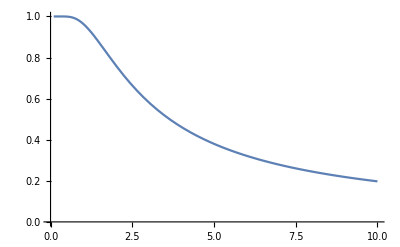

```mathematica
(* pe0 = -tanh(K/T) for some constant K; just assume K=2 for now without justification *)
Plot[Tanh[2/x],{x,0,10},PlotRange->{{0,10},{0,1}}]
```

```mathematica
h=6.63*^-34;
om=8.8043*^11;
k=1.38*^-23;
h*om/(2k)
```

21.1495

```mathematica
Tanh[0.2]//N
```

0.197375